```mathematica
ExtendableQ[G_Graph,t_Integer]:=With[{n=VertexCount[G]},EvenQ[n]&&t<n/2&&MissingQ@SelectFirst[Subsets[VertexList[G],{2t}],Length@FindIndependentEdgeSet@Subgraph[G,#]==t&&Length@FindIndependentEdgeSet@VertexDelete[G,#]!=n/2-t&]]
```

```mathematica
ExtendableCounterExample[G_Graph,t_Integer]:=With[{n=VertexCount[G]},EvenQ[n]&&t<n/2&&SelectFirst[Subsets[VertexList[G],{2t}],Length@FindIndependentEdgeSet@Subgraph[G,#]==t&&Length@FindIndependentEdgeSet@VertexDelete[G,#]!=n/2-t&,None]]
```

```mathematica
ExtendableQ[PetersenGraph[],1]
```

True

```mathematica
ExtendableCounterExample[PetersenGraph[],1]
```

None

```mathematica
test[g_]:=BipartiteGraphQ[g]||ExtendableQ[g,Ceiling[First@VertexDegree[g]/2]-1]
```

```mathematica
f[s_]:=Block[{t,n},t=StringSplit[s];n=StringLength@First@t;AdjacencyGraph/@Partition[Characters/@t/.{"0"->0,"1"->1},n]]
```

```mathematica
a=Join@@(f[Import["https://www.distanceregular.org/graphdata/"<>#,"String"]]&/@Select[StringSplit@Import["https://www.distanceregular.org/graphdata/"],StringEndsQ[".am"]]);
```

AdjacencyGraph::matsq: Argument {{0,1,1,1,1,1,1,0,0,0,«176»},{1,0,1,1,1,1,0,0,0,0,«176»},{1,1,0,1,1,1,0,0,0,0,«176»},{1,1,1,0,1,1,0,0,0,0,«176»},{1,1,1,1,0,1,0,0,0,0,«176»},{1,1,1,1,1,0,0,0,0,0,«176»},{1,0,0,0,0,0,0,1,1,1,«176»},{0,0,0,0,0,0,1,0,1,1,«176»},{0,0,0,0,0,0,1,1,0,1,«259»},{1,0,1,1,1,1,0,0,0,0,«176»},«176»} at position 2 is not a non-empty square matrix.

```mathematica
l=SortBy[Select[Cases[a,_Graph],EvenQ@VertexCount[#]&],VertexCount];
```

```mathematica
Export["distanceregular.g6",l]
```

distanceregular.g6

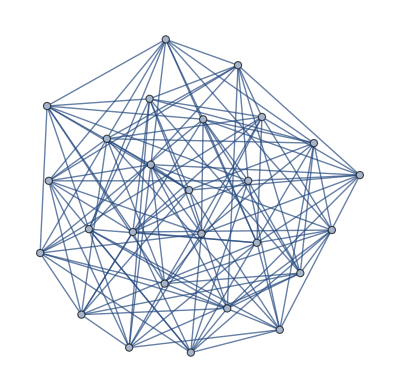
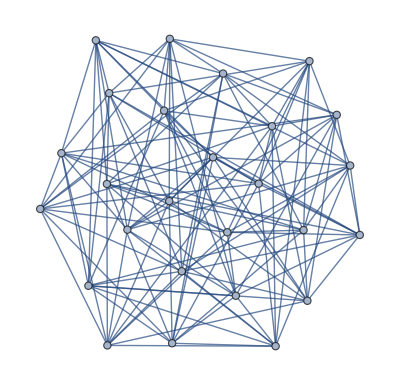
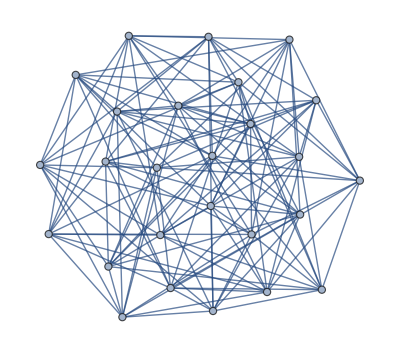
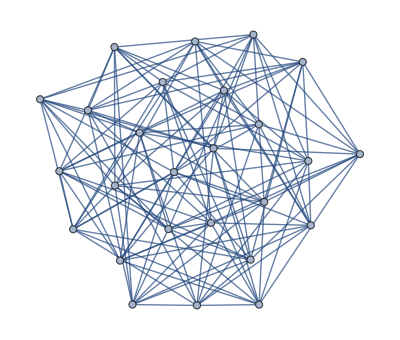
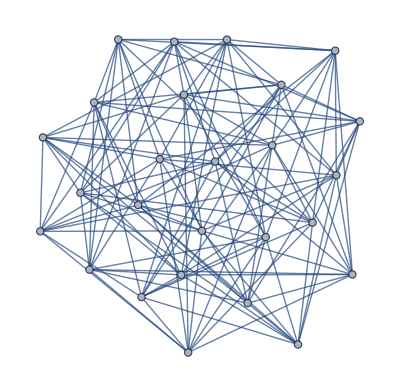
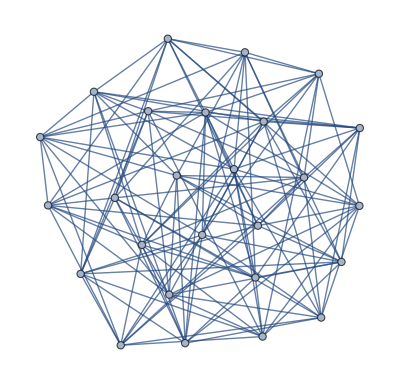
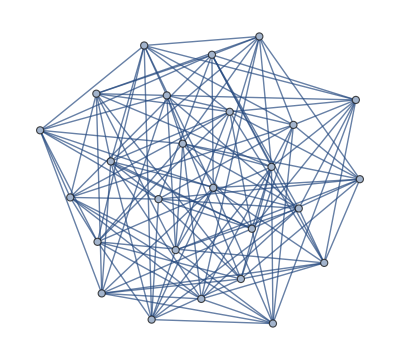
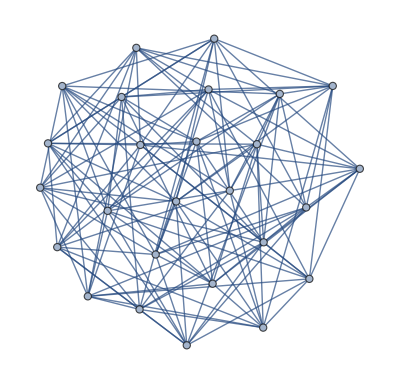

```mathematica
Select[l,!VertexTransitiveGraphQ[#]&]
```

```mathematica
VertexCount/@%
```

{26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,28,28,28,28,28,28,80,126,288}

```mathematica
ExtendableQ[G_Graph,t_Integer]/;VertexTransitiveGraphQ[G]:=Block[{n,s,o,r,a},n=VertexCount[G];
a=GraphAutomorphismGroup[G];
r={};Do[(If[DisjointQ[r,GroupOrbits[a,{s},Sort@PermutationReplace[#1,#2]&]],AppendTo[r,s]]),{s,Subsets[VertexList[G],{2t}]}];EvenQ[n]&&t<n/2&&MissingQ@SelectFirst[r,Length@FindIndependentEdgeSet@Subgraph[G,#]==t&&Length@FindIndependentEdgeSet@VertexDelete[G,#]!=n/2-t&]]
```

```mathematica
Monitor[Do[If[!test[g],Return[g]],{g,Select[l,VertexCount[#]<=20&]}],{g,VertexCount[g]}]
```

$Aborted

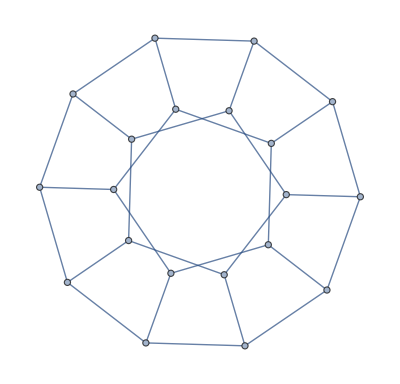
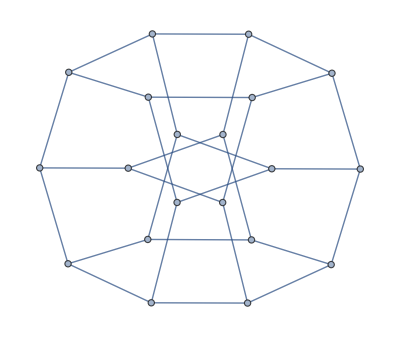
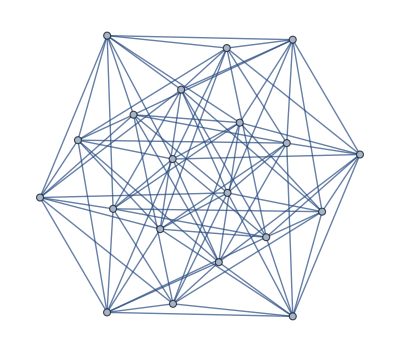
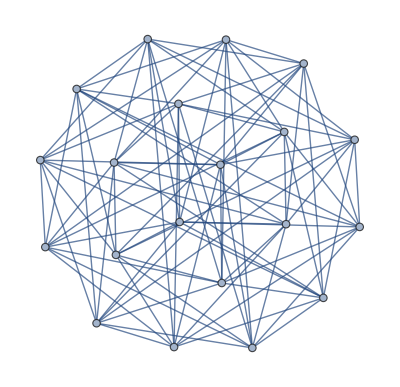

```mathematica
Select[l,VertexCount[#]==20&]
```

```mathematica
Block[{n,s,o,r,a,G,t},
G=-Graphics-;
t=Ceiling[First@VertexDegree[G]/2]-1;
n=VertexCount[G];
a=GraphAutomorphismGroup[G];
r={};
Monitor[Do[(If[DisjointQ[r,First@GroupOrbits[a,{s},Sort@PermutationReplace[#1,#2]&]],AppendTo[r,s]]),{s,Subsets[VertexList[G],{2t}]}],Length[r]];r]
```

$Aborted

```mathematica
GraphToString[g_Graph]:=GraphToString[g,2(Ceiling[First@VertexDegree[g]/2]-1)];
GraphToString[g_Graph,t_Integer]:=ToString@VertexCount[g]<>" "<>ToString[t]<>"\n"<>StringRiffle[StringJoin/@Map[ToString,Normal@AdjacencyMatrix[g],{2}],"\n"]
```

```mathematica
Export["distance_regular.txt",GraphToString[-Graphics-]]
```

distance_regular.txt

```mathematica
Export["kneser.txt",GraphToString[KneserGraph[9,4],26]]
```

kneser.txt

```mathematica
ConstantArray[0,{1,2}]
```

{{0,0}}

```mathematica
a={{3,3}};
```

```mathematica
Do[a⟦i,j⟧=1,{i,1},{j,2}]
```

```mathematica
a
```

{{1,1}}

```mathematica
ClearAll[knap];
knap[l_,t_]:=Module[{dp},dp[i_,j_]/;j<0:=0;dp[i_,0]:=1;
dp[0,j_]/;j>=1:=0;dp[i_,j_]:=dp[i,j]=dp[i-1,j]+dp[i-1,j-l⟦i⟧];Do[dp[i,j],{i,Length[l]},{j,t}];dp[Length[l],t]]
```

```mathematica
ClearAll[f];f[g_Graph]:=f[g,2(Ceiling[First@VertexDegree[g]/2]-1)];f[g_Graph,t_Integer]:=With[{n=VertexCount[g],a=GraphAutomorphismGroup[g]},Total[knap[#1,t]#2&@@@Tally[Sort/@(Length/@GroupOrbits[PermutationGroup[{#}],Range[n]]&/@GroupElements[GraphAutomorphismGroup[g]])]]/GroupOrder[a]]
```

```mathematica
f[-Graphics-]
```

154

```mathematica
f[KneserGraph[9,4],5]
```

$Aborted

```mathematica
l=Import["distanceregular.g6"];
```

```mathematica
Run["wsl ls"]
```

1